## Model of Cumulative Amplitude Histograms for Estimating Toxin Effects on Replenishment

This file covers the models in Figure 3A-D; E-F or Figure 4 are similar, except for different concentrations or normalization, respectively.

### Parameters

```mathematica
fibers=36; (*number of activated PFs*)
n0=3.; (*initial release sites*)
ne=3; (*extra release sites*)
p=0.6; (*initial p; altered p is set in the individual sections*)
q=8.*10^-12;
imax=49;  (*iterator*)
r=0.1; (*replenishment rate; altered r is set in the individual sections*)
isi=50*10^-3;
```

### Control

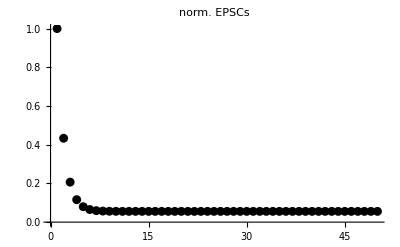

2.93333+0.1 x

1.62963+0.0555556 x

2.34667×10^-11+8.×10^-13 x

-Graphics-

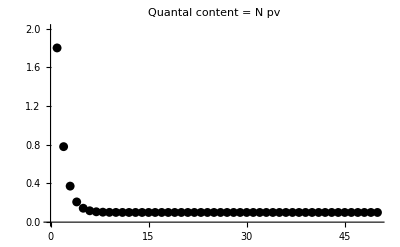

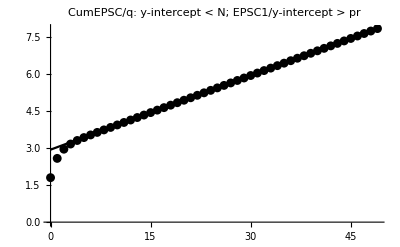

Real pr = 0.6

Real N = 3.

pr EPSC1/y-inter= 0.613636

pr Norm EPSC1/y-inter= 0.613636

y-inter = 2.93333

y-inter norm= 1.62963

slope = 0.1 x

slope norm= 0.0555556 x

Last EPSC ampl= 8.×10^-13

```mathematica
fibers=36; (*number of activated PFs*)
n0=3.; (*initial release sites*)
ne=3; (*extra release sites*)
p=0.6; (*initial p; altered p is set in the individual sections*)
q=8.*10^-12;
imax=49;  (*iterator*)
r=0.1; (*replenishment rate; altered r is set in the individual sections*)
isi=50*10^-3;

RRP=Join[
{n[0]=n0},
Table[
n[i]=n[i-1] -p*n[i-1]+r,{i,1,imax}
]];

rel=Table[
n[i] p,{i,0,imax}
];                                             (*quantal content, qc*)
epsc=rel*q;

(*Calculations for cumulative plot according to Schneggenburger & Neher*)
cum=Accumulate[rel];
cumepsc=Accumulate[epsc];
cum2=cum/rel[[1]];
tval=Table[t*isi,{t,50}];
cumt=Transpose[{tval,cum}];

(*SN plot*)
qcp1=ListPlot[rel,PlotRange->{0,2},PlotStyle->{Black,PointSize[0.016]},PlotLabel->"Quantal content = N pv"];
cp=ListPlot[cum,PlotRange->All,PlotLabel->"CumRel = CumEPSC/q: y-intercept < N;  EPSC1/y-intercept > pr"];
rp=ListPlot[RRP,PlotRange->All,PlotLabel->"RRP"];
ep=ListPlot[epsc,PlotRange->All,PlotLabel->"EPSCs"];
epn1=ListPlot[epsc/epsc[[1]],PlotRange->Full,PlotStyle->{Black,PointSize[0.016]},PlotLabel->"norm. EPSCs"]

(*generating the SN fit plot*)
xval=Table[x,{x,0,49}];
cn=Transpose[{xval,cum}];
cn2=Transpose[{xval,cum2}];
ce=Transpose[{xval,cumepsc}];

cnp=ListPlot[cn,PlotRange->All,PlotStyle->{Black,PointSize[0.016]},PlotLabel->"CumEPSC/q: y-intercept < N;  EPSC1/y-intercept > pr"];
cnp2=ListPlot[cn2,PlotRange->All,PlotStyle->{Black,PointSize[0.016]},PlotLabel->"CumEPSC/EPSC1: y-intercept < N;  EPSC1/y-intercept > pr"];
cep=ListPlot[ce,PlotRange->All,PlotLabel->"Cum EPSCs"];

line = Fit[Take[cn,-5], {1,x},x]
line2 = Fit[Take[cn2,-5], {1,x},x]
line3 = Fit[Take[ce,-5], {1,x},x]

lp=Plot[line,{x,0,49},PlotRange->All,PlotStyle->Black];
lp2=Plot[line2,{x,0,49},PlotRange->All,PlotStyle->Black];
lp3=Plot[line3,{x,0,49}];

(*Print["pr = ", (First[line]-n[1])/First[line]]*) (*No idea about this?*)

p1= cum[[1]]/First[line];
p2=cum2[[1]]/First[line2];
qcont1=p1 First[line];
qcont2=p2 First[line2];

Show[rp];
Show[ep];
Show[epn1]
Show[qcp1]
Show[cep,lp3];
Show[cnp,lp]
Show[cnp2,lp2];


Print["Real pr = ", p]
Print["Real N = ", n0]
Print["pr EPSC1/y-inter= ",p1]
Print["pr Norm EPSC1/y-inter= ", p2]
Print["y-inter = ",line[[1]]]
Print["y-inter norm= ",line2[[1]]]
Print["slope = ",line[[2]]]
Print["slope norm= ",line2[[2]]]
Print["Last EPSC ampl= ",epsc[[49]]]
(*Print["qcont1 = ",qcont1]
Print["qcont2 = ",qcont2]*)
```

### Control with temporary overfilling

Recordings in elevated Ca to rise pr

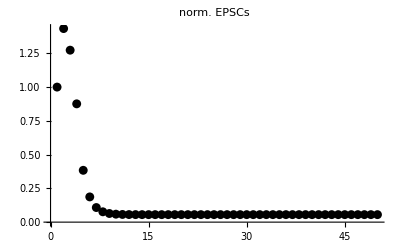

8.93333+0.1 x

4.96296+0.0555556 x

7.14667×10^-11+8.×10^-13 x

-Graphics-

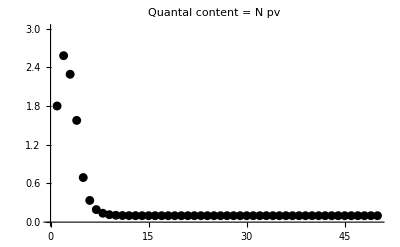

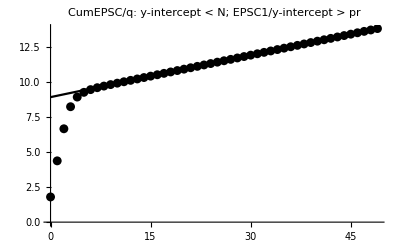

Real pr = 0.6

Real N = 3.

pr EPSC1/y-inter= 0.201493

pr Norm EPSC1/y-inter= 0.201493

y-inter = 8.93333

y-inter norm= 4.96296

slope = 0.1 x

slope norm= 0.0555556 x

Last EPSC ampl= 8.×10^-13

```mathematica
p=0.6; (*initial p; altered p is set in the individual sections*)
r=0.1; (*replenishment rate; altered r is set in the individual sections*)

RRP=Join[
{n[0]=n0},
Table[
n[i]=n[i-1] -p*n[i-1]+(ne-(i-1)) +r,{i,1,ne+1}
],
Table[
n[i]=n[i-1] -p*n[i-1] +r,{i,ne+1,imax}
]
];


rel=Table[
n[i] p,{i,0,imax}
];
epsc=rel*q;

(*Calculations for cumulative plot according to Schneggenburger & Neher*)
cum=Accumulate[rel];
cumepsc=Accumulate[epsc];
cum2=cum/rel[[1]];
tval=Table[t*isi,{t,50}];
cumt=Transpose[{tval,cum}];

(*SN plot*)
qcp1a=ListPlot[rel,PlotRange->{0,3},PlotStyle->{Black,PointSize[0.016]},PlotLabel->"Quantal content = N pv"];
cp=ListPlot[cum,PlotRange->All,PlotLabel->"CumRel = CumEPSC/q: y-intercept < N;  EPSC1/y-intercept > pr"];
rp=ListPlot[RRP,PlotRange->All,PlotLabel->"RRP"];
ep=ListPlot[epsc,PlotRange->All,PlotLabel->"EPSCs"];
epn1a=ListPlot[epsc/epsc[[1]],PlotRange->All,PlotRange->Full,PlotStyle->{Black,PointSize[0.016]},PlotLabel->"norm. EPSCs"]

(*generating the SN fit plot*)
xval=Table[x,{x,0,49}];
cn=Transpose[{xval,cum}];
cn2=Transpose[{xval,cum2}];
ce=Transpose[{xval,cumepsc}];

cnpo=ListPlot[cn,PlotRange->All,PlotStyle->{Black,PointSize[0.016]},PlotLabel->"CumEPSC/q: y-intercept < N;  EPSC1/y-intercept > pr"];
cnp2o=ListPlot[cn2,PlotRange->All,PlotStyle->{Black,PointSize[0.016]},PlotLabel->"CumEPSC/EPSC1: y-intercept < N;  EPSC1/y-intercept > pr"];
cepo=ListPlot[ce,PlotRange->All,PlotLabel->"Cum EPSCs"];

line = Fit[Take[cn,-5], {1,x},x]
line2 = Fit[Take[cn2,-5], {1,x},x]
line3 = Fit[Take[ce,-5], {1,x},x]

lpo=Plot[line,{x,0,49},PlotRange->All,PlotStyle->Black];
lp2o=Plot[line2,{x,0,49},PlotRange->All,PlotStyle->Black];
lp3o=Plot[line3,{x,0,49}];

p1= cum[[1]]/First[line];
p2=cum2[[1]]/First[line2];
qcont1=p1 First[line];
qcont2=p2 First[line2];

Show[rp];
Show[ep];
Show[epn1a]
Show[qcp1a]
Show[cepo,lp3o];
Show[cnpo,lpo]
Show[cnp2o,lp2o];


Print["Real pr = ", p]
Print["Real N = ", n0]
Print["pr EPSC1/y-inter= ",p1]
Print["pr Norm EPSC1/y-inter= ", p2]
Print["y-inter = ",line[[1]]]
Print["y-inter norm= ",line2[[1]]]
Print["slope = ",line[[2]]]
Print["slope norm= ",line2[[2]]]
Print["Last EPSC ampl= ",epsc[[49]]]
(*Print["qcont1 = ",qcont1]
Print["qcont2 = ",qcont2]*)
```

### CTx: Reduced repl. & unchnaged pr

Basic result in comparrison to control in plots normalized to 1st amplitude:
- slope decreases
- y-intercept unchanged

Recordings in elevated Ca to rise pr

2.96667+0.05 x

1.64815+0.0277778 x

2.37333×10^-11+4.×10^-13 x

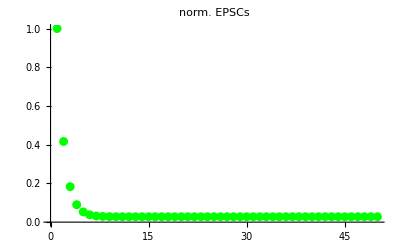

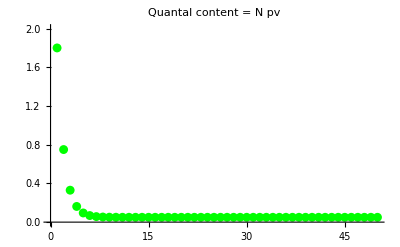

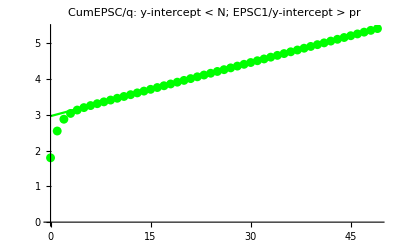

Real pr = 0.6

Real N = 3.

pr EPSC1/y-inter= 0.606742

pr Norm EPSC1/y-inter= 0.606742

y-inter = 2.96667

y-inter norm= 1.64815

slope = 0.05 x

slope norm= 0.0277778 x

Last EPSC ampl= 4.×10^-13

```mathematica
r=0.05;

RRP=Join[
{n[0]=n0},
Table[
n[i]=n[i-1] -p*n[i-1]+r,{i,1,imax}
]];

rel=Table[
n[i] p,{i,0,imax}
];
epsc=rel*q;

(*Calculations for cumulative plot according to Schneggenburger & Neher*)
cum=Accumulate[rel];
cumepsc=Accumulate[epsc];
cum2=cum/rel[[1]];
tval=Table[t*isi,{t,50}];
cumt=Transpose[{tval,cum}];

(*SN plot*)
qcp2=ListPlot[rel,PlotRange->{0,2},PlotStyle->{Green,PointSize[0.016]},PlotLabel->"Quantal content = N pv"];
cp=ListPlot[cum,PlotRange->All,PlotLabel->"CumRel = CumEPSC/q: y-intercept < N;  EPSC1/y-intercept > pr"];
rp=ListPlot[RRP,PlotRange->All,PlotLabel->"RRP"];
ep=ListPlot[epsc,PlotRange->All,PlotLabel->"EPSCs"];
epn2=ListPlot[epsc/epsc[[1]],PlotRange->All,PlotRange->Full,PlotStyle->{Green,PointSize[0.016]},PlotLabel->"norm. EPSCs"];

(*generating the SN fit plot*)
xval=Table[x,{x,0,49}];
cn=Transpose[{xval,cum}];
cn2=Transpose[{xval,cum2}];
ce=Transpose[{xval,cumepsc}];

cnpc=ListPlot[cn,PlotRange->All,PlotStyle->{Green,PointSize[0.016]}, PlotLabel->"CumEPSC/q: y-intercept < N;  EPSC1/y-intercept > pr"];
cnp2c=ListPlot[cn2,PlotRange->All,PlotStyle->{Green,PointSize[0.016]},PlotLabel->"CumEPSC/EPSC1: y-intercept < N;  EPSC1/y-intercept > pr"];
cep=ListPlot[ce,PlotRange->All,PlotLabel->"Cum EPSCs"];

line = Fit[Take[cn,-5], {1,x},x]
line2 = Fit[Take[cn2,-5], {1,x},x]
line3 = Fit[Take[ce,-5], {1,x},x]

lpc=Plot[line,{x,0,49},PlotRange->All,PlotStyle->Green];
lp2c=Plot[line2,{x,0,49},PlotRange->All,PlotStyle->Green];
lp3=Plot[line3,{x,0,49}];

(*Print["pr = ", (First[line]-n[1])/First[line]]*) (*No idea about this?*)

p1= cum[[1]]/First[line];
p2=cum2[[1]]/First[line2];
qcont1=p1 First[line];
qcont2=p2 First[line2];

Show[rp];
Show[epn2]
Show[qcp2]
Show[cep,lp3];
Show[cnpc,lpc]
Show[cnp2c,lp2c];


Print["Real pr = ", p]
Print["Real N = ", n0]
Print["pr EPSC1/y-inter= ",p1]
Print["pr Norm EPSC1/y-inter= ", p2]
Print["y-inter = ",line[[1]]]
Print["y-inter norm= ",line2[[1]]]
Print["slope = ",line[[2]]]
Print["slope norm= ",line2[[2]]]
Print["Last EPSC ampl= ",epsc[[49]]]
(*Print["qcont1 = ",qcont1]
Print["qcont2 = ",qcont2]*)
```

### CTx: Reduced repl. & unchnaged pr with temporary overfilling

Basic result in comparrison to control in plots normalized to 1st amplitude:
- slope decreases
- y-intercept unchanged

Recordings in elevated Ca to rise pr

8.96667+0.05 x

4.98148+0.0277778 x

7.17333×10^-11+4.×10^-13 x

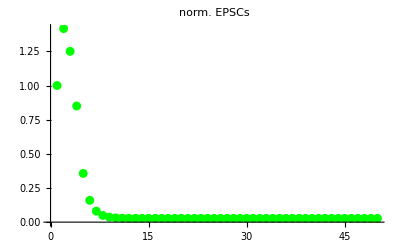

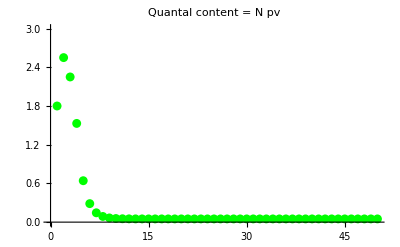

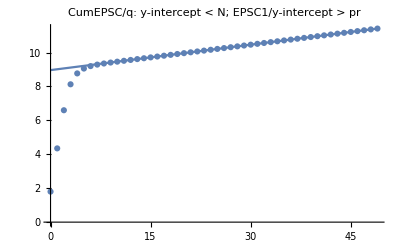

Real pr = 0.6

Real N = 3.

pr EPSC1/y-inter= 0.200743

pr Norm EPSC1/y-inter= 0.200743

y-inter = 8.96667

y-inter norm= 4.98148

slope = 0.05 x

slope norm= 0.0277778 x

Last EPSC ampl= 4.×10^-13

```mathematica
r=0.05;

RRP=Join[
{n[0]=n0},
Table[
n[i]=n[i-1] -p*n[i-1]+(ne-(i-1)) +r,{i,1,ne+1}
],
Table[
n[i]=n[i-1] -p*n[i-1] +r,{i,ne+1,imax}
]
];

rel=Table[
n[i] p,{i,0,imax}
];
epsc=rel*q;

(*Calculations for cumulative plot according to Schneggenburger & Neher*)
cum=Accumulate[rel];
cumepsc=Accumulate[epsc];
cum2=cum/rel[[1]];
tval=Table[t*isi,{t,50}];
cumt=Transpose[{tval,cum}];

(*SN plot*)
qcp2a=ListPlot[rel,PlotRange->{0,3},PlotStyle->{Green,PointSize[0.016]},PlotLabel->"Quantal content = N pv"];
cp=ListPlot[cum,PlotRange->All,PlotLabel->"CumRel = CumEPSC/q: y-intercept < N;  EPSC1/y-intercept > pr"];
rp=ListPlot[RRP,PlotRange->All,PlotLabel->"RRP"];
ep=ListPlot[epsc,PlotRange->All,PlotLabel->"EPSCs"];
epn2a=ListPlot[epsc/epsc[[1]],PlotRange->All,PlotRange->Full,PlotStyle->{Green,PointSize[0.016]},PlotLabel->"norm. EPSCs"];

(*generating the SN fit plot*)
xval=Table[x,{x,0,49}];
cn=Transpose[{xval,cum}];
cn2=Transpose[{xval,cum2}];
ce=Transpose[{xval,cumepsc}];

cnpco=ListPlot[cn,PlotRange->All, PlotLabel->"CumEPSC/q: y-intercept < N;  EPSC1/y-intercept > pr"];
cnp2co=ListPlot[cn2,PlotRange->All,PlotStyle->{Green,PointSize[0.016]},PlotLabel->"CumEPSC/EPSC1: y-intercept < N;  EPSC1/y-intercept > pr"];
cep=ListPlot[ce,PlotRange->All,PlotLabel->"Cum EPSCs"];

line = Fit[Take[cn,-5], {1,x},x]
line2 = Fit[Take[cn2,-5], {1,x},x]
line3 = Fit[Take[ce,-5], {1,x},x]

lpco=Plot[line,{x,0,49}];
lp2co=Plot[line2,{x,0,49},PlotRange->All,PlotStyle->Green];
lp3=Plot[line3,{x,0,49}];

(*Print["pr = ", (First[line]-n[1])/First[line]]*) (*No idea about this?*)

p1= cum[[1]]/First[line];
p2=cum2[[1]]/First[line2];
qcont1=p1 First[line];
qcont2=p2 First[line2];

Show[rp];
Show[epn2a]
Show[qcp2a]
Show[cep,lp3];
Show[cnpco,lpco]
Show[cnp2c,lp2c];


Print["Real pr = ", p]
Print["Real N = ", n0]
Print["pr EPSC1/y-inter= ",p1]
Print["pr Norm EPSC1/y-inter= ", p2]
Print["y-inter = ",line[[1]]]
Print["y-inter norm= ",line2[[1]]]
Print["slope = ",line[[2]]]
Print["slope norm= ",line2[[2]]]
Print["Last EPSC ampl= ",epsc[[49]]]
(*Print["qcont1 = ",qcont1]
Print["qcont2 = ",qcont2]*)
```

### AgTx: Strongly reduced pr & unchanged repl.

Basic result in comparrison to control in plots normalized to 1st amplitude:
- slope increases
- y-intercept increases

Recordings in elevated Ca to rise pr

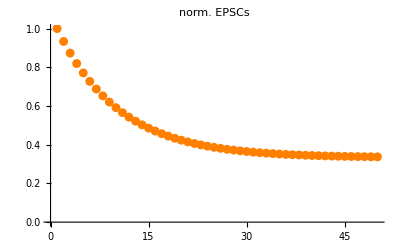

2.02372+0.101349 x

6.74573+0.337831 x

1.61898×10^-11+8.10794×10^-13 x

-Graphics-

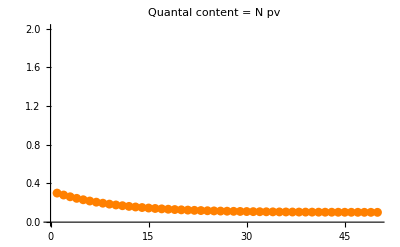

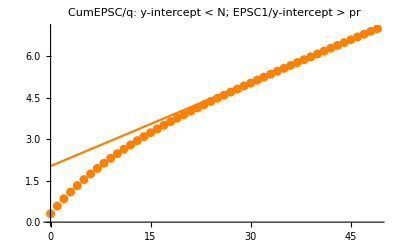

Real pr = 0.1

Real N = 3.

pr EPSC1/y-inter= 0.148242

pr Norm EPSC1/y-inter= 0.148242

y-inter = 2.02372

y-inter norm= 6.74573

slope = 0.101349 x

slope norm= 0.337831 x

Last EPSC ampl= 8.1018×10^-13

```mathematica
p=0.1;
r=0.1;

RRP=Join[
{n[0]=n0},
Table[
n[i]=n[i-1] -p*n[i-1]+r,{i,1,imax}
]];

rel=Table[
n[i] p,{i,0,imax}
];
epsc=rel*q;

(*Calculations for cumulative plot according to Schneggenburger & Neher*)
cum=Accumulate[rel];
cumepsc=Accumulate[epsc];
cum2=cum/rel[[1]];
tval=Table[t*isi,{t,50}];
cumt=Transpose[{tval,cum}];

(*SN plot*)
qcp3=ListPlot[rel,PlotRange->{0,2},PlotStyle->{Orange,PointSize[0.016]},PlotLabel->"Quantal content = N pv"];
cp=ListPlot[cum,PlotRange->All,PlotLabel->"CumRel = CumEPSC/q: y-intercept < N;  EPSC1/y-intercept > pr"];
rp=ListPlot[RRP,PlotRange->All,PlotLabel->"RRP"];
ep=ListPlot[epsc,PlotRange->All,PlotLabel->"EPSCs"];
epn3=ListPlot[epsc/epsc[[1]],PlotRange->All,PlotRange->Full,PlotStyle->{Orange,PointSize[0.016]},PlotLabel->"norm. EPSCs"]

(*generating the SN fit plot*)
xval=Table[x,{x,0,49}];
cn=Transpose[{xval,cum}];
cn2=Transpose[{xval,cum2}];
ce=Transpose[{xval,cumepsc}];

cnpa=ListPlot[cn,PlotRange->All,PlotStyle->{Orange,PointSize[0.016]}, PlotLabel->"CumEPSC/q: y-intercept < N;  EPSC1/y-intercept > pr"];
cnp2a=ListPlot[cn2,PlotRange->All,PlotStyle->{Orange,PointSize[0.016]},PlotLabel->"CumEPSC/EPSC1: y-intercept < N;  EPSC1/y-intercept > pr"];
cep=ListPlot[ce,PlotRange->All,PlotLabel->"Cum EPSCs"];

line = Fit[Take[cn,-5], {1,x},x]
line2 = Fit[Take[cn2,-5], {1,x},x]
line3 = Fit[Take[ce,-5], {1,x},x]

lpa=Plot[line,{x,0,49},PlotStyle->Orange];
lp2a=Plot[line2,{x,0,49},PlotStyle->Orange];
lp3=Plot[line3,{x,0,49}];

(*Print["pr = ", (First[line]-n[1])/First[line]]*) (*No idea about this?*)

p1= cum[[1]]/First[line];
p2=cum2[[1]]/First[line2];
qcont1=p1 First[line];
qcont2=p2 First[line2];

Show[rp];
Show[epn3]
Show[qcp3]
Show[cep,lp3];
Show[cnpa,lpa]
Show[cnp2a,lp2a];


Print["Real pr = ", p]
Print["Real N = ", n0]
Print["pr EPSC1/y-inter= ",p1]
Print["pr Norm EPSC1/y-inter= ", p2]
Print["y-inter = ",line[[1]]]
Print["y-inter norm= ",line2[[1]]]
Print["slope = ",line[[2]]]
Print["slope norm= ",line2[[2]]]
Print["Last EPSC ampl= ",epsc[[49]]]
```

### AgTx: Strongly reduced pr & unchnaged repl. with temporary overfilling

Basic result in comparrison to control in plots normalized to 1st amplitude:
- slope increases
- y-intercept increases

Recordings in elevated Ca to rise pr

7.7501+0.106189 x

25.8337+0.353963 x

6.20008×10^-11+8.49512×10^-13 x

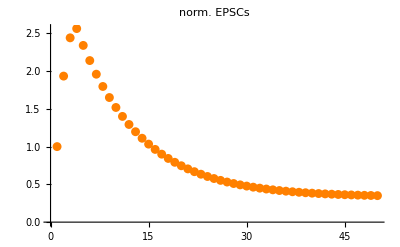

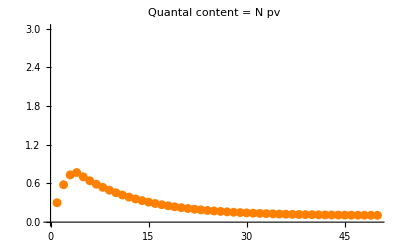

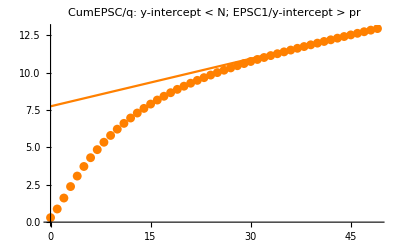

Real pr = 0.1

Real N = 3.

pr EPSC1/y-inter= 0.0387092

pr Norm EPSC1/y-inter= 0.0387092

y-inter = 7.7501

y-inter norm= 25.8337

slope = 0.106189 x

slope norm= 0.353963 x

Last EPSC ampl= 8.46698×10^-13

```mathematica
p=0.1;
r=0.1;

RRP=Join[
{n[0]=n0},
Table[
n[i]=n[i-1] -p*n[i-1]+(ne-(i-1)) +r,{i,1,ne+1}
],
Table[
n[i]=n[i-1] -p*n[i-1] +r,{i,ne+1,imax}
]
];

rel=Table[
n[i] p,{i,0,imax}
];
epsc=rel*q;

(*Calculations for cumulative plot according to Schneggenburger & Neher*)
cum=Accumulate[rel];
cumepsc=Accumulate[epsc];
cum2=cum/rel[[1]];
tval=Table[t*isi,{t,50}];
cumt=Transpose[{tval,cum}];

(*SN plot*)
qcp3a=ListPlot[rel,PlotRange->{0,3},PlotStyle->{Orange,PointSize[0.016]},PlotLabel->"Quantal content = N pv"];
cp=ListPlot[cum,PlotRange->All,PlotLabel->"CumRel = CumEPSC/q: y-intercept < N;  EPSC1/y-intercept > pr"];
rp=ListPlot[RRP,PlotRange->All,PlotLabel->"RRP"];
ep=ListPlot[epsc,PlotRange->All,PlotLabel->"EPSCs",PlotStyle->{Orange,PointSize[0.016]}];
epn3a=ListPlot[epsc/epsc[[1]],PlotRange->All,PlotRange->Full,PlotStyle->{Orange,PointSize[0.016]},PlotLabel->"norm. EPSCs"];

(*generating the SN fit plot*)
xval=Table[x,{x,0,49}];
cn=Transpose[{xval,cum}];
cn2=Transpose[{xval,cum2}];
ce=Transpose[{xval,cumepsc}];

cnpao=ListPlot[cn,PlotRange->All,PlotStyle->{Orange,PointSize[0.016]}, PlotLabel->"CumEPSC/q: y-intercept < N;  EPSC1/y-intercept > pr"];
cnp2ao=ListPlot[cn2,PlotRange->All,PlotStyle->{Orange,PointSize[0.016]},PlotLabel->"CumEPSC/EPSC1: y-intercept < N;  EPSC1/y-intercept > pr"];
cep=ListPlot[ce,PlotRange->All,PlotLabel->"Cum EPSCs"];

line = Fit[Take[cn,-5], {1,x},x]
line2 = Fit[Take[cn2,-5], {1,x},x]
line3 = Fit[Take[ce,-5], {1,x},x]

lpao=Plot[line,{x,0,49},PlotStyle->Orange];
lp2ao=Plot[line2,{x,0,49},PlotStyle->Orange];
lp3=Plot[line3,{x,0,49}];

(*Print["pr = ", (First[line]-n[1])/First[line]]*) (*No idea about this?*)

p1= cum[[1]]/First[line];
p2=cum2[[1]]/First[line2];
qcont1=p1 First[line];
qcont2=p2 First[line2];

Show[rp];
Show[epn3a]
Show[qcp3a]
Show[cep,lp3];
Show[cnpao,lpao]
Show[cnp2ao,lp2ao];


Print["Real pr = ", p]
Print["Real N = ", n0]
Print["pr EPSC1/y-inter= ",p1]
Print["pr Norm EPSC1/y-inter= ", p2]
Print["y-inter = ",line[[1]]]
Print["y-inter norm= ",line2[[1]]]
Print["slope = ",line[[2]]]
Print["slope norm= ",line2[[2]]]
Print["Last EPSC ampl= ",epsc[[49]]]
(*Print["qcont1 = ",qcont1]
Print["qcont2 = ",qcont2]*)
```

### Comparing w/o overfilling

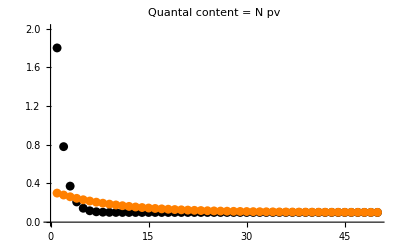

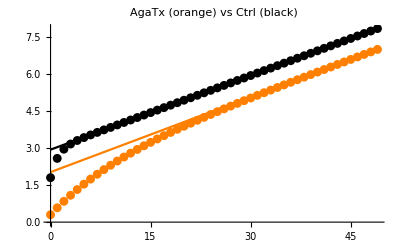

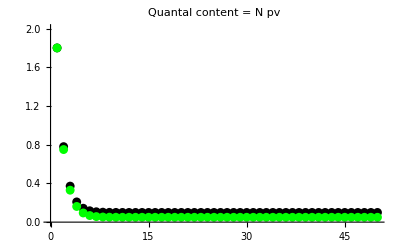

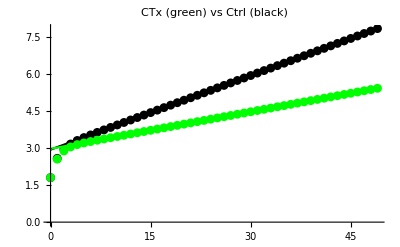

```mathematica
Show[qcp1,qcp3]
Show[cnp,lp,cnpa,lpa,PlotLabel->"AgaTx (orange) vs Ctrl (black)"(*,AxesLabel->{"Stim #","Cum qunatal content"}*)]

Show[qcp1,qcp2]
Show[cnp,lp,cnpc,lpc,PlotLabel->"CTx (green) vs Ctrl (black)"(*,AxesLabel->{"Stim #","Cum qunatal content"}*)]
```

### Comparing with overfilling

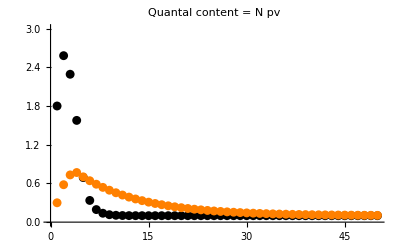

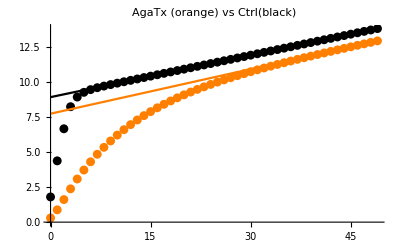

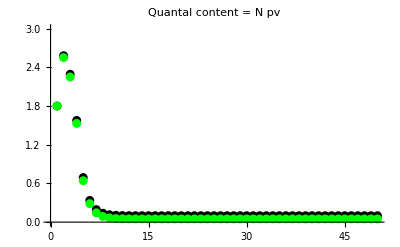

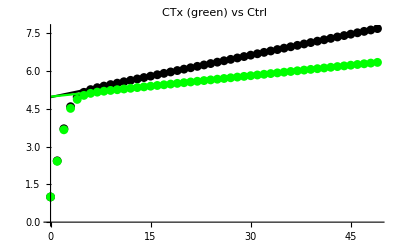

```mathematica
Show[qcp1a,qcp3a]
Show[cnpo,lpo,cnpao,lpao,PlotLabel->"AgaTx (orange) vs Ctrl(black)"(*,AxesLabel->{"Stim #","Cum quantal content"}*)]

Show[qcp1a,qcp2a]
Show[cnp2o,lp2o,cnp2co,lp2co,PlotLabel->"CTx (green) vs Ctrl"(*,AxesLabel->{"Stim #","Quantal content"}*)]
```